```mathematica
Clear[K1]
Clear[K2]
Clear[K3]
```

```mathematica
L=3;
l=2;
```

```mathematica
Clear[x];
Clear[y];
solution = Factor[Simplify[Solve[
Sqrt[(L/2-x)^2+(l/2-y)^2]-Sqrt[(-L/2-x)^2+(l-y)^2]==K1 &&
Sqrt[(L/2-x)^2+(l/2-y)^2]-Sqrt[(-L/2-x)^2+y^2]==K2 &&
Sqrt[(-L/2-x)^2+(l-y)^2]-Sqrt[(-L/2-x)^2+y^2]==K3
,{x,y}]]]
```

{}

```mathematica
getK1[x_,y_]:=Sqrt[(L/2-x)^2+(l/2-y)^2]-Sqrt[(-L/2-x)^2+(l-y)^2];
getK2[x_,y_]:=Sqrt[(L/2-x)^2+(l/2-y)^2]-Sqrt[(-L/2-x)^2+y^2];
getK3[x_,y_]:=Sqrt[(-L/2-x)^2+(l-y)^2]-Sqrt[(-L/2-x)^2+y^2];
```

```mathematica
getX1[K2_,K3_]:=-(-12+6 K3^2+3 K2^2 K3^2-3 K2 K3^3-√(-(-10+K2^2) (-2 K2+K3)^2 (-4+K3^2) (-10+K2^2-2 K2 K3+K3^2)))/(4 (-18+2 K2^2-2 K2 K3+5 K3^2))
```

```mathematica
getY1[K2_,K3_]:=(-144 K2+16 K2^3+72 K3-56 K2^2 K3+4 K2^4 K3+80 K2 K3^2-8 K2^3 K3^2-28 K3^3+5 K2^2 K3^3-K2 K3^4+3 K3 √(-(-10+K2^2) (-2 K2+K3)^2 (-4+K3^2) (-10+K2^2-2 K2 K3+K3^2)))/(4 (2 K2-K3) (-18+2 K2^2-2 K2 K3+5 K3^2))
```

```mathematica
getX2[K2_,K3_]:=-(-12+6 K3^2+3 K2^2 K3^2-3 K2 K3^3+√(-(-10+K2^2) (-2 K2+K3)^2 (-4+K3^2) (-10+K2^2-2 K2 K3+K3^2)))/(4 (-18+2 K2^2-2 K2 K3+5 K3^2))
```

```mathematica
getY2[K2_,K3_]:=(-144 K2+16 K2^3+72 K3-56 K2^2 K3+4 K2^4 K3+80 K2 K3^2-8 K2^3 K3^2-28 K3^3+5 K2^2 K3^3-K2 K3^4-3 K3 √(-(-10+K2^2) (-2 K2+K3)^2 (-4+K3^2) (-10+K2^2-2 K2 K3+K3^2)))/(4 (2 K2-K3) (-18+2 K2^2-2 K2 K3+5 K3^2))
```

```mathematica
getX3[K1_,K3_]:=-(-12+6 K3^2+3 K1^2 K3^2+3 K1 K3^3+√(-(-10+K1^2) (2 K1+K3)^2 (-4+K3^2) (-10+K1^2+2 K1 K3+K3^2)))/(4 (-18+2 K1^2+2 K1 K3+5 K3^2))
```

```mathematica
getY3[K1_,K3_]:=(-144 K1+16 K1^3-72 K3-8 K1^2 K3+4 K1^4 K3+16 K1 K3^2+8 K1^3 K3^2+12 K3^3+5 K1^2 K3^3+K1 K3^4-3 K3 √(-(-10+K1^2) (2 K1+K3)^2 (-4+K3^2) (-10+K1^2+2 K1 K3+K3^2)))/(4 (2 K1+K3) (-18+2 K1^2+2 K1 K3+5 K3^2))
```

```mathematica
getX4[K1_,K3_]:=-(-12+6 K3^2+3 K1^2 K3^2+3 K1 K3^3-√(-(-10+K1^2) (2 K1+K3)^2 (-4+K3^2) (-10+K1^2+2 K1 K3+K3^2)))/(4 (-18+2 K1^2+2 K1 K3+5 K3^2))
```

```mathematica
getY4[K1_,K3_]:=(-144 K1+16 K1^3-72 K3-8 K1^2 K3+4 K1^4 K3+16 K1 K3^2+8 K1^3 K3^2+12 K3^3+5 K1^2 K3^3+K1 K3^4+3 K3 √(-(-10+K1^2) (2 K1+K3)^2 (-4+K3^2) (-10+K1^2+2 K1 K3+K3^2)))/(4 (2 K1+K3) (-18+2 K1^2+2 K1 K3+5 K3^2))
```

```mathematica
getX5[K1_,K2_]:=-(-12+6 K1^2-12 K1 K2+3 K1^3 K2+6 K2^2-6 K1^2 K2^2+3 K1 K2^3+√(-(-10+K1^2) (K1+K2)^2 (-10+K2^2) (-4+K1^2-2 K1 K2+K2^2)))/(4 (-18+5 K1^2-8 K1 K2+5 K2^2))
```

```mathematica
getY5[K1_,K2_]:=-1/(4 (K1+K2) (-18+5 K1^2-8 K1 K2+5 K2^2))(72 K1-28 K1^3+72 K2+4 K1^2 K2+K1^4 K2+20 K1 K2^2+K1^3 K2^2-12 K2^3-K1^2 K2^3-K1 K2^4-3 K1 √(-(-10+K1^2) (K1+K2)^2 (-10+K2^2) (-4+K1^2-2 K1 K2+K2^2))+3 K2 √(-(-10+K1^2) (K1+K2)^2 (-10+K2^2) (-4+K1^2-2 K1 K2+K2^2)))
```

```mathematica
getX6[K1_,K2_]:=-(-12+6 K1^2-12 K1 K2+3 K1^3 K2+6 K2^2-6 K1^2 K2^2+3 K1 K2^3-√(-(-10+K1^2) (K1+K2)^2 (-10+K2^2) (-4+K1^2-2 K1 K2+K2^2)))/(4 (-18+5 K1^2-8 K1 K2+5 K2^2))
```

```mathematica
getY6[K1_,K2_]:=-1/(4 (K1+K2) (-18+5 K1^2-8 K1 K2+5 K2^2))(72 K1-28 K1^3+72 K2+4 K1^2 K2+K1^4 K2+20 K1 K2^2+K1^3 K2^2-12 K2^3-K1^2 K2^3-K1 K2^4+3 K1 √(-(-10+K1^2) (K1+K2)^2 (-10+K2^2) (-4+K1^2-2 K1 K2+K2^2))-3 K2 √(-(-10+K1^2) (K1+K2)^2 (-10+K2^2) (-4+K1^2-2 K1 K2+K2^2)))
```

```mathematica
test[]:=Module[{x=RandomReal[{-L/2,L/2}],y=RandomReal[{0,l}],K1,K2,K3,tabX={}, tabY={}},
K1=getK1[x,y];
K2=getK2[x,y];
K3=getK3[x,y];
Print["K1=",K1,"  K2=",K2,"  K3=",K3];
tabX={
getX1[K2,K3],getX2[K2,K3],
getX3[K1,K3],getX4[K1,K3],
getX5[K1,K2],getX6[K1,K2]
};
tabY={
getY1[K2,K3],getY2[K2,K3],
getY3[K1,K3],getY4[K1,K3],
getY5[K1,K2],getY6[K1,K2]
};
Print["x : ",x," ",tabX];
Print["y : ",y," ",tabY];
]
```

```mathematica
test[]
```

K1=0.577508  K2=1.79539  K3=1.21788

x : -0.850594 {-0.850594,0.939495,0.939495,-0.850594,0.939495,-0.850594}

y : 0.21301 {0.21301,2.96928,2.96928,0.21301,2.96928,0.21301}

```mathematica
testGraphique[]:=(
Print[ListPlot[
Table[Table[
{getX1[getK2[x,y],getK3[x,y]],getY1[getK2[x,y],getK3[x,y]]}
,{x,-L/2,-L/4,0.1}],{y,l/2+0.5,l/2+0.51,0.1}]
,AspectRatio->0.5,AxesOrigin->{-L/2,0},PlotRange->{{-L/2,L/2},{0,l}}]];
Print[ListPlot[
Table[Table[
{getX2[getK2[x,y],getK3[x,y]],getY2[getK2[x,y],getK3[x,y]]}
,{x,-L/2,-L/4,0.1}],{y,l/2+0.5,l/2+0.51,0.1}]
,AspectRatio->0.5,AxesOrigin->{-L/2,0},PlotRange->{{-L/2,L/2},{0,l}}]];
)
```

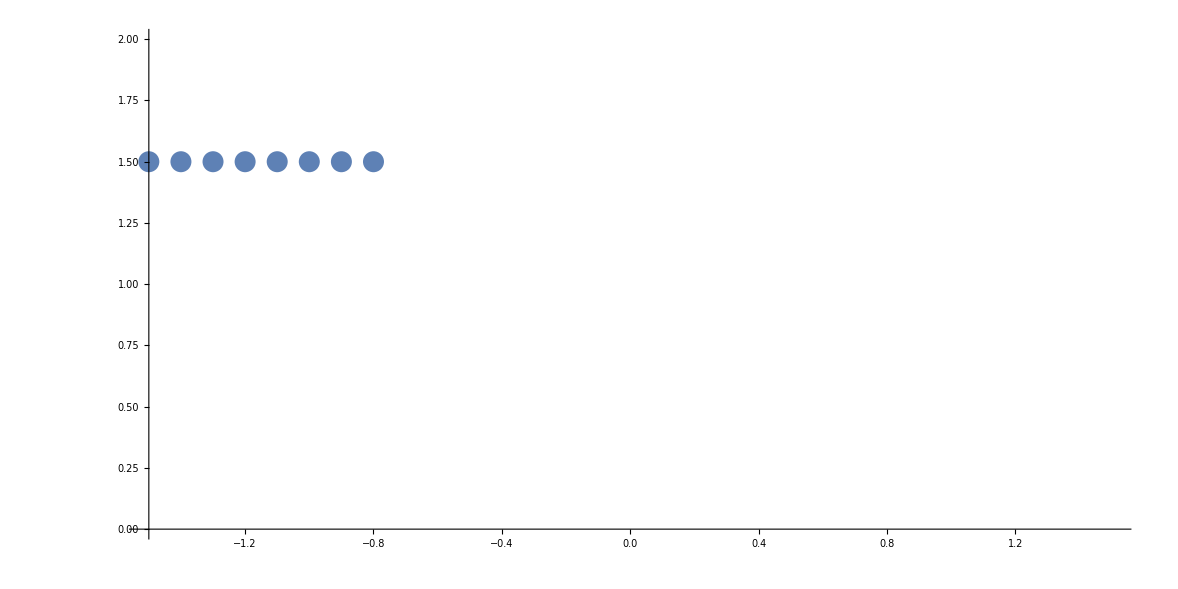

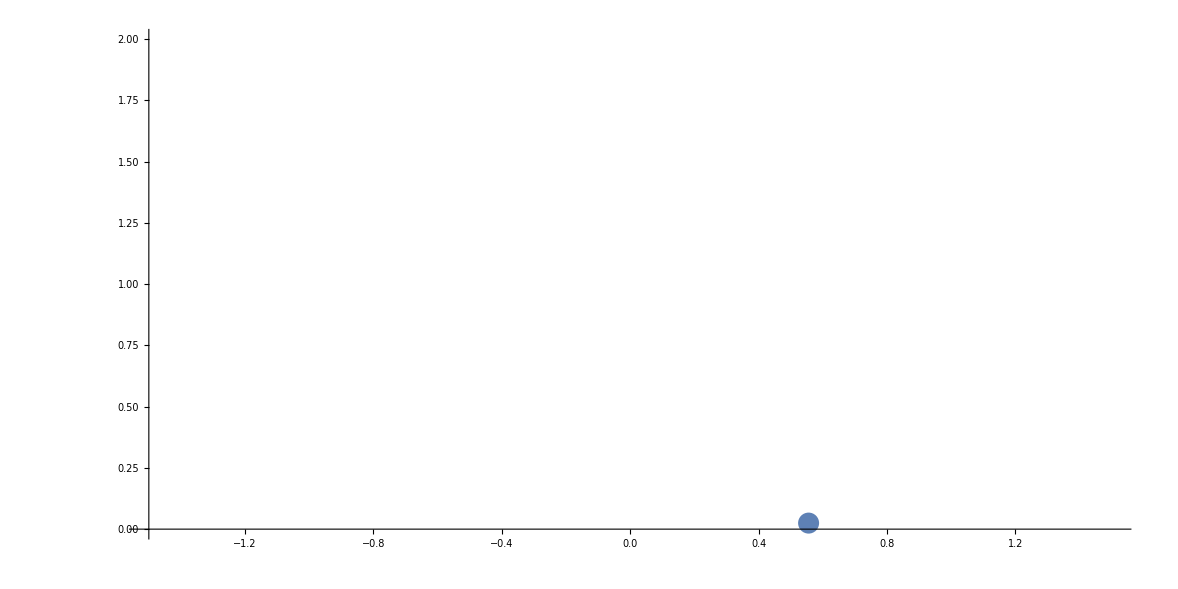

```mathematica
testGraphique[]
```

```mathematica
f[x_,T_]:=If[Mod[x,T]<T/2,-2.5,2.5]
```

```mathematica
fp = 1/40000;
```

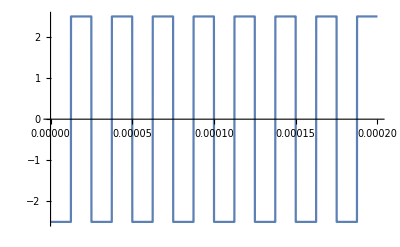

```mathematica
Plot[f[x,fp],{x,0,1/5000}]
```

```mathematica
amplitude = 2.5;
frequenceP = 40000;
frequenceM = 100;
```

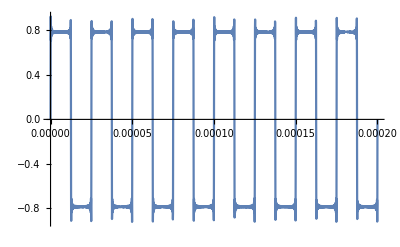

```mathematica
Plot[Sum[Sin[2*Pi*frequenceP*i*x]/i,{i,1,100,2}],{x,0,1/5000}]
```

```mathematica
Seuil :=1.6;
```

```mathematica
condition[x_,y_]:=
(Abs[Sqrt[(x-1.5)^2+(y-2)^2]-Sqrt[(x-1.5)^2+y^2]]<Seuil)&&
(Abs[Sqrt[(x-1.5)^2+(y-2)^2]-Sqrt[(x+1.5)^2+(y-1)^2]]<Seuil)&&
(Abs[Sqrt[(x-1.5)^2+y^2]-Sqrt[(x+1.5)^2+(y-1)^2]]<Seuil);
```

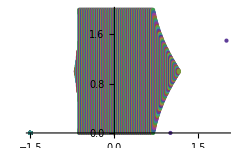

```mathematica
ListPlot[Append[Table[
{If[condition[x,y],x,-1.5]
,If[condition[x,y],y,0]}
, {x,-1.5,1.5,0.01}, {y, 0, 2, 0.01}],{0,1.5}]]
```

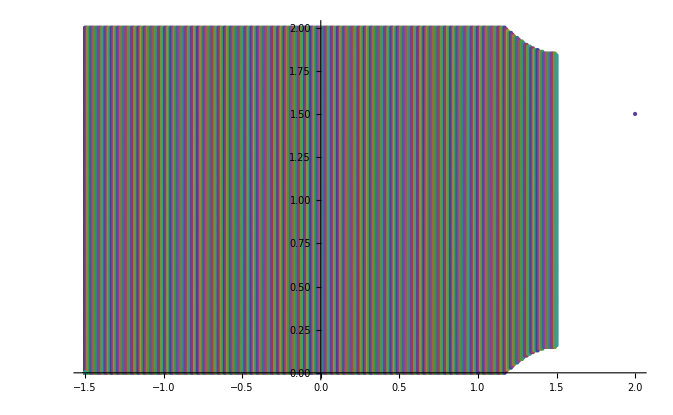
```mathematica
d1 - d2;-Graphics-
```

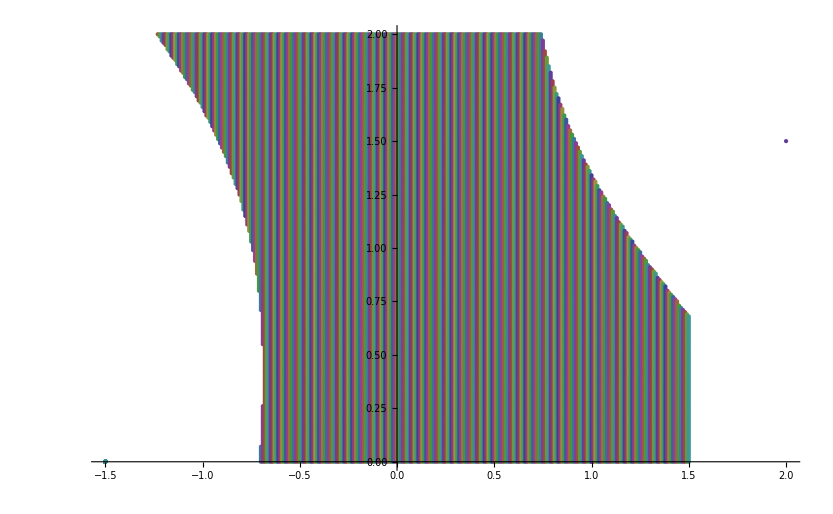
```mathematica
d1-d3-Graphics-
```

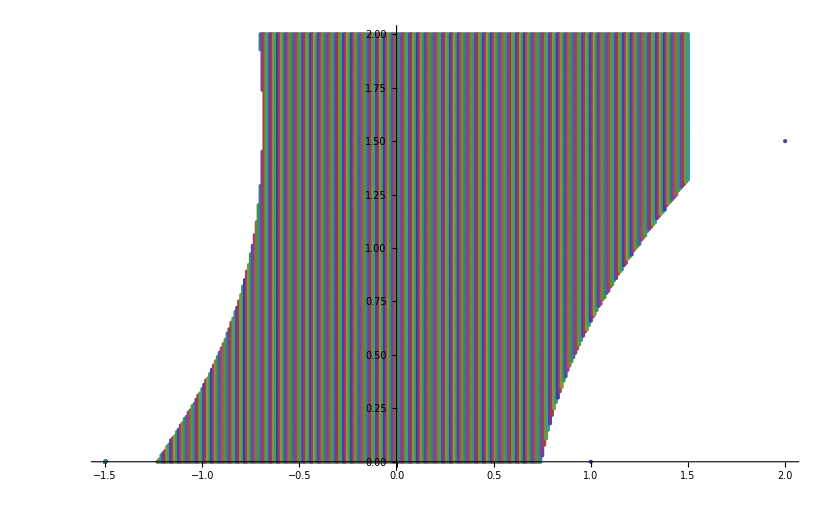
```mathematica
d2-d3-Graphics-
```